Settings (phi = 0.0 rad):  tA=0.000 ps,  tB=1.552 ps,  tA'=3.104 ps,  tB'=10.865 ps  (T=12.417 ps)

GammaH=0.667 ps^-1,  GammaL=0.667 ps^-1,  ΔΓ=0.000 ps^-1,  C=1.

Window half-width sigmaWin = 0.3 ps

Selected counts:  AB=25600   A'B=7325   AB'=45   A'B'=15

Total pairs selected (across all four settings) = 32985

--- CHSH (empirical, picture probabilities) ---

E(AB)=-303/400  E(A'B)=-5193/7325  E(AB')=-11/15  E(A'B')=11/15

S_empirical = -2.933

--- CHSH (theory, averaging exact times of selected pairs) ---

S_theory_from_selected_pairs = S_fromPairs

S_theory_at_markers = S_markers  (max |S| ≤ 2.828 at this geometry)

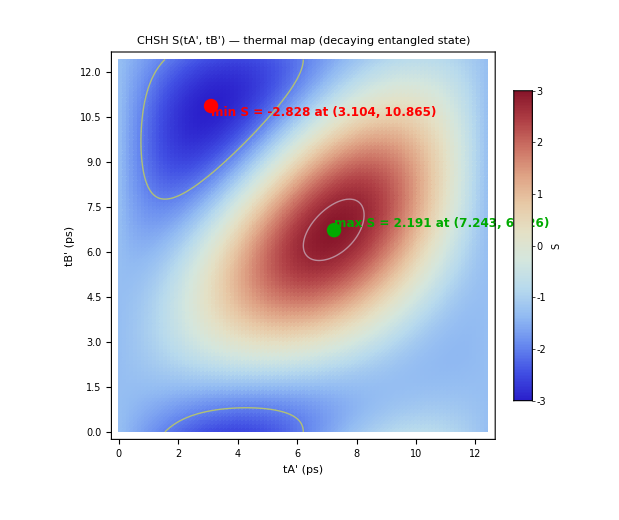

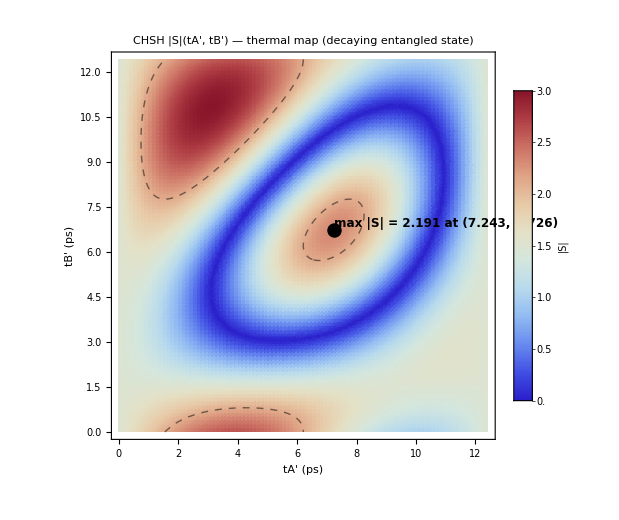

Max S = 2.191 at  tA'=7.243 ps,  tB'=6.726 ps

Min S = -2.828 at  tA'=3.104 ps,  tB'=10.865 ps

Max |S| = 2.191 at  tA'=7.243 ps,  tB'=6.726 ps

```mathematica
(* ::Package::*)(*
========================1) Clear& parameters (unnormalized)========================*)ClearAll["Global`*"];
Quiet@Needs["PlotLegends`"]; (*for BarLegend/Legended*)

(*---Mixing& decay parameters---*)
deltaM=0.506;             (*ps^-1*)
tauAvg=1.5;               (*mean lifetime~1/GammaAvg,ps*)
GammaAvg=1/tauAvg;        (*ps^-1*)
dGamma=0.0;               (*ΔΓ=Γ_H-Γ_L (ps^-1);set>0 to see time-varying entanglement*)
GammaH=GammaAvg+dGamma/2;   (*ps^-1*)
GammaL=GammaAvg-dGamma/2;   (*ps^-1*)
Cmix=1.0;                 (*C= |p|^2/|q|^2;C=1->CP conservation*)

T=2 Pi/deltaM;            (*oscillation period (ps)*)

(*---Time-selection window& ensemble---*)
sigmaWin=0.3;             (*ps,half-window*)
nPairs=1000000;         (*ensemble size*)

(*----CHSH settings----*)
phi=0.;
tWrap[t_]:=Mod[t,T];
tA=tWrap[phi/deltaM];
tB=tWrap[(phi+Pi/4)/deltaM];
tAp=tWrap[(phi+Pi/2)/deltaM];
tBp=tWrap[(phi-Pi/4)/deltaM];

(* ========================2) Probabilities from the figure========================*)
sumExpHL[t1_?NumericQ,t2_?NumericQ]:=Exp[-(GammaH t1+GammaL t2)]+Exp[-(GammaL t1+GammaH t2)];

xi[t1_?NumericQ,t2_?NumericQ]:=Cos[deltaM (t1-t2)]/Cosh[dGamma (t1-t2)/2];

PBB[t1_?NumericQ,t2_?NumericQ]:=(Cmix/8)*sumExpHL[t1,t2]*(1-xi[t1,t2]);   (*B^0,B^0*)
PBbB[t1_?NumericQ,t2_?NumericQ]:=(1/8)*sumExpHL[t1,t2]*(1+xi[t1,t2]);   (*B^0,B̄^0*)
PBbBrev[t1_?NumericQ,t2_?NumericQ]:=(1/8)*sumExpHL[t1,t2]*(1+xi[t1,t2]);   (*B̄^0,B^0*)
PBbBb[t1_?NumericQ,t2_?NumericQ]:=(1/(8 Cmix))*sumExpHL[t1,t2]*(1-xi[t1,t2]);   (*B̄^0,B̄^0*)

EfromP[t1_?NumericQ,t2_?NumericQ]:=Module[{pp=PBB[t1,t2],pm=PBbB[t1,t2],mp=PBbBrev[t1,t2],mm=PBbBb[t1,t2]},Re@Chop[(pp+mm-pm-mp)/(pp+pm+mp+mm)]];

Smarkers[tA_?NumericQ,tAp_?NumericQ,tB_?NumericQ,tBp_?NumericQ]:=EfromP[tA,tB]+EfromP[tAp,tB]+EfromP[tA,tBp]-EfromP[tAp,tBp];

(* ========================3) Ensemble with proper H/L widths========================*)
SeedRandom[20250828];
expSample[gamma_]:=-Log[1-RandomReal[]]/gamma;

pairs=Table[If[RandomReal[]<1/2,<|"id"->i,"tL"->expSample[GammaL],"tR"->expSample[GammaH]|>,<|"id"->i,"tL"->expSample[GammaH],"tR"->expSample[GammaL]|>],{i,nPairs}];

Print["Settings (phi = ",NumberForm[phi,{3,1}]," rad):  tA=",NumberForm[tA,{5,3}]," ps,  tB=",NumberForm[tB,{5,3}]," ps,  tA'=",NumberForm[tAp,{5,3}]," ps,  tB'=",NumberForm[tBp,{5,3}]," ps  (T=",NumberForm[T,{5,3}]," ps)"];
Print["GammaH=",NumberForm[GammaH,{4,3}]," ps^-1,  GammaL=",NumberForm[GammaL,{4,3}]," ps^-1,  ΔΓ=",NumberForm[dGamma,{4,3}]," ps^-1,  C=",Cmix];
Print["Window half-width sigmaWin = ",sigmaWin," ps"];

(* ========================4) Select pairs in the four windows========================*)
within[t_,c_]:=Abs[t-c]<=sigmaWin;
combos={{"AB",tA,tB},{"ApB",tAp,tB},{"ABp",tA,tBp},{"ApBp",tAp,tBp}};
buckets=<|"AB"->{},"ApB"->{},"ABp"->{},"ApBp"->{}|>;

Scan[Function[p,Module[{tL=p["tL"],tR=p["tR"],matches,best},matches=Select[combos,within[tL,#[[2]]]&&within[tR,#[[3]]]&];
If[matches=!={},best=First@SortBy[matches,Abs[tL-#[[2]]]+Abs[tR-#[[3]]]&];
buckets[best[[1]]]=Append[buckets[best[[1]]],{tL,tR}]];]],pairs];

qAB=Length[buckets["AB"]];qApB=Length[buckets["ApB"]];
qABp=Length[buckets["ABp"]];qApBp=Length[buckets["ApBp"]];
totalSelected=qAB+qApB+qABp+qApBp;

Print["Selected counts:  AB=",qAB,"   A'B=",qApB,"   AB'=",qABp,"   A'B'=",qApBp];
Print["Total pairs selected (across all four settings) = ",totalSelected];

(* ========================5) CHSH from these pairs========================*)
sampleOutcomeFromPicture[t1_?NumericQ,t2_?NumericQ]:=Module[{w={PBB[t1,t2],PBbB[t1,t2],PBbBrev[t1,t2],PBbBb[t1,t2]}},RandomChoice[w->{{1,1},{1,-1},{-1,1},{-1,-1}}]];

empiricalE[plist_List]:=If[Length[plist]==0,Missing["NoData"],Mean@(Times@@@(sampleOutcomeFromPicture[#[[1]],#[[2]]]&/@plist))];

theoryE[plist_List]:=If[Length[plist]==0,Missing["NoData"],Mean@(EfromP[#[[1]],#[[2]]]&/@plist)];

EABemp=empiricalE[buckets["AB"]];
EApBemp=empiricalE[buckets["ApB"]];
EABpemp=empiricalE[buckets["ABp"]];
EApBpemp=empiricalE[buckets["ApBp"]];

EABth=theoryE[buckets["AB"]];
EApBth=theoryE[buckets["ApB"]];
EABpth=theoryE[buckets["ABp"]];
EApBpth=theoryE[buckets["ApBp"]];

haveEmp=VectorQ[{EABemp,EApBemp,EABpemp,EApBpemp},NumericQ];
haveTh=VectorQ[{EABth,EApBth,EABpth,EApBpth},NumericQ];

If[haveEmp,Semp=N[EABemp+EApBemp+EABpemp-EApBpemp,6];
Print["--- CHSH (empirical, picture probabilities) ---"];
Print["E(AB)=",NumberForm[EABemp,{5,3}],"  E(A'B)=",NumberForm[EApBemp,{5,3}],"  E(AB')=",NumberForm[EABpemp,{5,3}],"  E(A'B')=",NumberForm[EApBpemp,{5,3}]];
Print["S_empirical = ",NumberForm[Semp,{6,3}]],Print["Not enough data in one or more buckets to form S_empirical."]];

If[haveTh,S_fromPairs=N[EABth+EApBth+EABpth-EApBpth,6];
Print["--- CHSH (theory, averaging exact times of selected pairs) ---"];
Print["S_theory_from_selected_pairs = ",NumberForm[S_fromPairs,{6,3}]],Print["Not enough data in one or more buckets to form S_theory_from_selected_pairs."]];

S_markers=N[Smarkers[tA,tAp,tB,tBp],10];
Print["S_theory_at_markers = ",NumberForm[S_markers,{6,4}],"  (max |S| ≤ 2.828 at this geometry)"];

(* ========================6) 2D thermal heatmaps for S and|S| ========================*)
sRange={0,T};
constraints=sRange[[1]]<=u<=sRange[[2]]&&sRange[[1]]<=v<=sRange[[2]];

(*Locate extrema over the domain*)
maxData=NMaximize[{Smarkers[tA,u,tB,v],constraints},{u,v}];
minData=NMinimize[{Smarkers[tA,u,tB,v],constraints},{u,v}];
absData=NMaximize[{Abs[Smarkers[tA,u,tB,v]],constraints},{u,v}];

maxS=maxData[[1]];{uMax,vMax}={u,v}/. maxData[[2]];
minS=minData[[1]];{uMin,vMin}={u,v}/. minData[[2]];
maxAbsS=absData[[1]];{uAbs,vAbs}={u,v}/. absData[[2]];

(*Symmetric scale for S;nonnegative for|S|*)
sMin=-3;sMax=3;
absMin=0;absMax=3;

(*---Heatmap for S---*)
sHeat=DensityPlot[Smarkers[tA,u,tB,v],{u,sRange[[1]],sRange[[2]]},{v,sRange[[1]],sRange[[2]]},ColorFunction->"ThermometerColors",ColorFunctionScaling->True,PlotRange->{sMin,sMax},Frame->True,FrameLabel->{"tA' (ps)","tB' (ps)"},PlotLabel->"CHSH S(tA', tB') — thermal map (decaying entangled state)",PlotPoints->100,MaxRecursion->2,ImageSize->520];

boundsS=ContourPlot[Smarkers[tA,u,tB,v],{u,sRange[[1]],sRange[[2]]},{v,sRange[[1]],sRange[[2]]},Contours->{-2,2},ContourStyle->{Directive[Yellow,Thick],Directive[LightBlue,Thick]},ContourShading->False,Frame->False,Axes->False,PlotPoints->100,MaxRecursion->2];

markersS=Graphics[{Darker[Green],PointSize[.02],Point[{uMax,vMax}],Inset[Style[Row[{"max S = ",NumberForm[maxS,{5,3}]," at (",NumberForm[uMax,{5,3}],", ",NumberForm[vMax,{5,3}],")"}],12,Bold],{uMax,vMax},{Left,Bottom}],Red,PointSize[.02],Point[{uMin,vMin}],Inset[Style[Row[{"min S = ",NumberForm[minS,{5,3}]," at (",NumberForm[uMin,{5,3}],", ",NumberForm[vMin,{5,3}],")"}],12,Bold],{uMin,vMin},{Left,Top}]}];

sHeatLegend=Legended[Show[sHeat,boundsS,markersS,PlotRange->All],Placed[BarLegend[{"ThermometerColors",{sMin,sMax}},LegendLabel->"S"],Right]];

Print[sHeatLegend];

(*---Heatmap for|S|---*)
absHeat=DensityPlot[Abs[Smarkers[tA,u,tB,v]],{u,sRange[[1]],sRange[[2]]},{v,sRange[[1]],sRange[[2]]},ColorFunction->"ThermometerColors",ColorFunctionScaling->True,PlotRange->{absMin,absMax},Frame->True,FrameLabel->{"tA' (ps)","tB' (ps)"},PlotLabel->"CHSH |S|(tA', tB') — thermal map (decaying entangled state)",PlotPoints->100,MaxRecursion->2,ImageSize->520];

boundsAbs=ContourPlot[Abs[Smarkers[tA,u,tB,v]],{u,sRange[[1]],sRange[[2]]},{v,sRange[[1]],sRange[[2]]},Contours->{2},ContourStyle->{Directive[Black,Thick,Dashed]},ContourShading->False,Frame->False,Axes->False,PlotPoints->100,MaxRecursion->2];

markerAbs=Graphics[{Black,PointSize[.02],Point[{uAbs,vAbs}],Inset[Style[Row[{"max |S| = ",NumberForm[maxAbsS,{5,3}]," at (",NumberForm[uAbs,{5,3}],", ",NumberForm[vAbs,{5,3}],")"}],12,Bold],{uAbs,vAbs},{Left,Bottom}]}];

absHeatLegend=Legended[Show[absHeat,boundsAbs,markerAbs,PlotRange->All],Placed[BarLegend[{"ThermometerColors",{absMin,absMax}},LegendLabel->"|S|"],Right]];

Print[absHeatLegend];

Print["Max S = ",NumberForm[maxS,{6,3}]," at  tA'=",NumberForm[uMax,{5,3}]," ps,  tB'=",NumberForm[vMax,{5,3}]," ps"];
Print["Min S = ",NumberForm[minS,{6,3}]," at  tA'=",NumberForm[uMin,{5,3}]," ps,  tB'=",NumberForm[vMin,{5,3}]," ps"];
Print["Max |S| = ",NumberForm[maxAbsS,{6,3}]," at  tA'=",NumberForm[uAbs,{5,3}]," ps,  tB'=",NumberForm[vAbs,{5,3}]," ps"];
```